## Get helper functions

```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"UTILITY_readBeamFiles.nb"}]]
```

## Import

```mathematica
fileName= FileNameJoin[{NotebookDirectory[],"beams/optimizerRunningBestBeam_PENT.h5"}];
fileName= "~/twoBunch.h5";



data = readBeamFile[fileName];
(*{driverData,witnessData} = getDriverAndWitness[data];*)
```

```mathematica
(*data=Table[
AssociateTo[row,"z"->-3*^8*row["t"]],
{row,data}
];*)
```

```mathematica
data = RandomSample[data,10000];
```

### Optional: Remove outliers

```mathematica
Length[data]
```

10000

```mathematica
data = DeleteAnomalies[data];
```

```mathematica
Length[data]
```

9793

## Visualize

```mathematica
densityHistogramMod[10^6{#x,#px/#pz}&/@data,{100,100},LabelStyle->20,ImageSize->400]
densityHistogramMod[10^6{#x,#y}&/@data,{100,100},LabelStyle->20,ImageSize->400]
(*densityHistogramMod[{#x,#px/#pz}&/@driverData,{100,100}(*,LabelStyle->20,ImageSize->800*)]
densityHistogramMod[{#x,#px/#pz}&/@witnessData,{100,100}(*,LabelStyle->20,ImageSize->800*)]*)
```

-Graphics-

-Graphics-

```mathematica
densityHistogramMod[{10^6#z,10^-9#pz}&/@data,{100,100},LabelStyle->20,ImageSize->400]
```

-Graphics-

```mathematica
densityHistogramMod[{10^-9#pz,10^6#x}&/@data,{100,100},LabelStyle->20,ImageSize->400]
densityHistogramMod[{10^-9#pz,10^6#px/#pz}&/@data,{100,100},LabelStyle->20,ImageSize->400]
```

-Graphics-

-Graphics-

1046.32

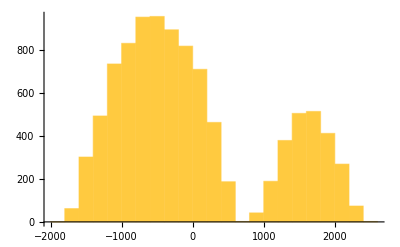

```mathematica
StandardDeviation[10^6 data[[All,"z"]]]
Histogram[10^6 data[[All,"z"]]]
```

```mathematica
StandardDeviation[10^-6 data[[All,"pz"]]]
```

0.539993

```mathematica
Button["Plot",

 img3D=ListPointPlot3D[
{10^3#x,10^-9#pz,10^3#px/#pz}&/@data,
(*{10^3#x,10^3#z,10^3#y}&/@data,*)
SphericalRegion->True,
ImageSize->800,
(*ColorFunction->"Rainbow",*)
ColorFunction->(ColorData["Rainbow"][#2]&),
BoxRatios->{1,1,1},
PlotRange->All,
AxesLabel->{"x [mm]","pz [GeV]","x' [mrad]"},
(*AxesLabel->{"x [mm]","z [mm]","y [mm]"},*)
LabelStyle->20,
AxesStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3]}
];
Print[img3D]

]
```

Plot

-Graphics3D-

#### Animation

```mathematica
(*Preferred method*)

(*(x, x', energy)*)
(*2025-04-18 NMM comment: Make sure the color scale is right before using this block. 
If not 
replace 
ColorFunction->"Rainbow", 
with 
ColorFunction->(ColorData["Rainbow"][#2]&),
*)
(*imgArr=ParallelTable[
Rasterize[
ListPointPlot3D[
{10^3#x,10^3#px/#pz,10^-9#pz}&/@data,
SphericalRegion->True,
ImageSize->800,
ColorFunction->"Rainbow",
BoxRatios->{1,1,1},
PlotRange->All,
AxesLabel->{"x [mm]","pz [GeV]","x' [mrad]"},
LabelStyle->20,
AxesStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3]},
ViewPoint->{Cos[ϕ],0.75,Sin[ϕ]},
ViewVertical->{0,1,0}
],
RasterSize->800
],
{ϕ,0,2π,π/32}
];*)

(*(y, y', z)*)
(*imgArr=ParallelTable[
Rasterize[
ListPointPlot3D[
{10^3#y,10^3#z,10^3#py/#pz}&/@data,
SphericalRegion->True,
ImageSize->800,
ColorFunction->(ColorData["Rainbow"][#2]&),
BoxRatios->{1,1,1},
PlotRange->All,
AxesLabel->{"y [mm]","z [mm]","y' [mrad]"},
LabelStyle->20,
AxesStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3]},
ViewPoint->{Cos[ϕ],0.75,Sin[ϕ]},
ViewVertical->{0,1,0}
],
RasterSize->800
],
{ϕ,0,2π,π/32}
];*)

(*(x, x', z)*)
(*imgArr=ParallelTable[
Rasterize[
ListPointPlot3D[
{10^3#x,10^3#z,10^3#px/#pz}&/@data,
SphericalRegion->True,
ImageSize->800,
ColorFunction->(ColorData["Rainbow"][#2]&),
BoxRatios->{1,1,1},
PlotRange->All,
AxesLabel->{"x [mm]","z [mm]","x' [mrad]"},
LabelStyle->20,
AxesStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3]},
ViewPoint->{Cos[ϕ],0.75,Sin[ϕ]},
ViewVertical->{0,1,0}
],
RasterSize->800
],
{ϕ,0,2π,π/32}
];
Export["~/anim.gif",imgArr]*)

(*(x, z, E)*)
(*imgArr=ParallelTable[
Rasterize[
ListPointPlot3D[
{10^3#x,10^3#z,10^-9#pz}&/@data,
SphericalRegion->True,
ImageSize->800,
ColorFunction->(ColorData["Rainbow"][#3]&),
BoxRatios->{1,1,1},
PlotRange->All,
AxesLabel->{"x [mm]","z [mm]","Energy [GeV]"},
LabelStyle->20,
AxesStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3]},
ViewPoint->{Cos[ϕ],0.75,Sin[ϕ]},
ViewVertical->{0,1,0}
],
RasterSize->800
],
{ϕ,0,2π,π/32}
];

Export["~/anim.gif",imgArr]*)
```

~/anim.gif

```mathematica
(*Legacy methods*)
(*
img3D = ListPointPlot3D[{#x,#px/#pz,#pz}&/@data,ImageSize->800,ColorFunction->"Rainbow",BoxRatios->{1,1,1},PlotRange->All,LabelStyle->20,Ticks->None]

tourSteps =Table[
Scaled[{2*Cos[ϕ],2*Sin[ϕ],0}],
{ϕ,0,2π,π/32}
];

Parallelize[Tour3DVideo[img3D,tourSteps]]*)

(*
tourVid = Parallelize[Tour3DVideo[img3D]]

Export[
"~/x_xp_pz.gif",
VideoFrameList[tourVid,100]
]*)
```

## Linear propagation

```mathematica
ClearAll[z]
```

```mathematica
Plot[
Evaluate[10^6{
StandardDeviation[
(#x + z*#px/#pz)&/@driverData
],
StandardDeviation[
(#x + z*#px/#pz)&/@witnessData
],
StandardDeviation[
(#y + z*#py/#pz)&/@driverData
],
StandardDeviation[
(#y + z*#py/#pz)&/@witnessData
]
}],

{z,-2,2},

PlotStyle->{{ColorData[97][1]},{ColorData[97][1],Dashed},{ColorData[97][2]},{ColorData[97][2],Dashed}},
(*PlotLegends->{"σ_(x, driver) [μm]","σ_(x, witness) [μm]","σ_(y, driver) [μm]","σ_(y, witness) [μm]"},*)
PlotLegends->{"x, driver", "x, witness","y, driver","y, witness"},
PlotRange->{0,250},
ImageSize->800,
LabelStyle->20,
Frame->True,
FrameLabel->{"z from PENT [m]","σ [μm]"}
]

Plot[
Evaluate[1/1.349*10^6{
InterquartileRange[
(#x + z*#px/#pz)&/@driverData
],
InterquartileRange[
(#x + z*#px/#pz)&/@witnessData
],
InterquartileRange[
(#y + z*#py/#pz)&/@driverData
],
InterquartileRange[
(#y + z*#py/#pz)&/@witnessData
]
}],

{z,-2,2},

PlotStyle->{{ColorData[97][1]},{ColorData[97][1],Dashed},{ColorData[97][2]},{ColorData[97][2],Dashed}},
PlotLegends->{"x, driver", "x, witness","y, driver","y, witness"},
PlotRange->{0,250},
ImageSize->800,
LabelStyle->20,
Frame->True,
FrameLabel->{"z from PENT [m]", "IQR implied σ [μm]"}
]
```

-Graphics-

-Graphics-

```mathematica
+
```